### Chapter XIII Creating Figures and Diagrams with Graphics Primitives

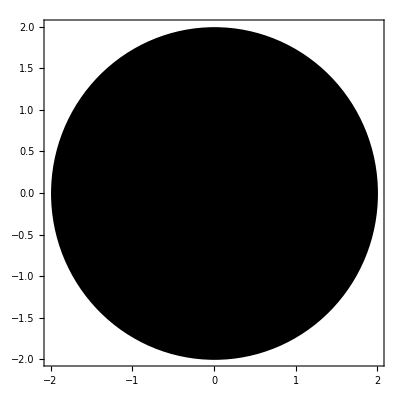

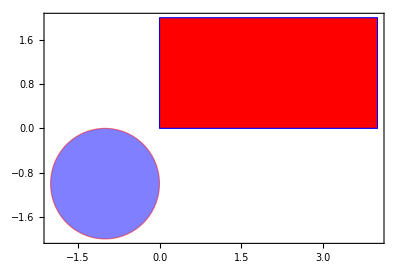

```mathematica
Graphics[Disk[{0,0},2],PlotRange->6,Frame->True]
Graphics[{Red,EdgeForm[Blue],Rectangle[{0,0},{4,2}],Blue,Opacity[0.5],EdgeForm[{Red,Thick,Dashed}],Disk[{-1,-1}]},PlotRange->6,Frame->True]
```

```mathematica
DynamicModule[{d,x,t},Manipulate[Graphics[{Disk[{x[t],d[t]}],Rectangle[{0,-0.5},{50,0}]},PlotRange->{{-1,50},{-1,50}},PlotLabel->ToString[d[t]]<>" meters"],{t,0,3.2},Initialization:>{(d[t_]:=1/2(-9.8)t^2+50),(x[t_]:=10t)}]]
```

```mathematica
Graphics3D[{Sphere[],Opacity[0.5],Sphere[{1,0.5,1}]},Boxed->False]
```

-Graphics3D-

```mathematica
Manipulate[Graphics3D[{Blue,Opacity[0.5],Sphere[{0,0,0},1],Green,Opacity[0.5],Sphere[{x,y,z},1]},PlotRange->2,Boxed->False],{x,-1,1},{y,-1,1},{z,-1,1}]
```

```mathematica
DynamicModule[{d,x,y,t},Manipulate[
Graphics3D[{Sphere[{x[t],y[t],d[t]}],Polygon[{{0,0,0},{0,20,0},{20,20,0},{20,0,0}}]},PlotRange->{{0,20},{0,20},{0,50}},PlotLabel->ToString[d[t]]<>" meters",Boxed->False,Lighting->"Accent"],{t,0,3.2},Initialization :>{(d[t_]:=1/2(-9.8) t^2+50 ),(x[t_]:=5t),(y[t_]:=5t)}]]
```